# Análise de Séries Temporais e Predições com Redes Neurais

## Introdução

Neste projeto apresento uma introdução ao uso de redes neurais como ferramenta auxiliar na modelagem de séries temporais. Primeiro, diversas funções importantes para análise “clássica” de séries temporais, além da inicialização de redes neurais long short-term memory usando a biblioteca de redes neurais do Mathematica. Em seguida, apresento três aplicações, na seguinte ordem: primeiro, utilizo um exemplo de série temporal em que, apesar de clara tendência sazonal, as redes neurais não conseguem predizer um número significativo de pontos no futuro. Este exemplo é utilizado para mostrar a importância de um bom pré-processamento “clássico” das séries. Segundamente, mostro um exemplo onde o pré-processamento de uma série temporal é bem sucedido, levando a um processo de predição razoável. Por último, mostro um exemplo em que uma série temporal é extremamente difícil de ser predita por intervenções externas irregulares, independentes de pré-processamento.

## Definindo Funções úteis

### Differencing

Função que retorna uma série de diferenças normalizada pela média da  série original

```mathematica
differencing[data_]:=Differences[data]/Mean[data]
```

### Detrending

Função que recebe lista como input e retorna tupla com fit linear, série já sem tendência e plot

```mathematica
detrending[data_]:=Module[{t,linearFit,detrended},
{linearFit,detrended}={
LinearModelFit[data,t,t],
MapThread[#2 - linearFit[#1]&,{Range[Length[data]],data}]
}
]
```

### Cross-Correlation

Correlação cruzada entre duas séries

```mathematica
crossCorrelation[data1_,data2_,lag_]:=Sum[(data1[[i]]-Mean[data1]) (data2[[i+lag]]-Mean[data2]),{i,Length[data1]-lag}]/(StandardDeviation[data1] StandardDeviation[data2] (Length[data1]-lag))
```

### Relevant Peaks

Função recebe série e retorna lista de pares {posição do pico, altura do pico}. Possível especificar um threshold para mínima altura de picos relevantes (Default = 2/(√Length[data])).

```mathematica
relevantPeaks[data_,σ_,s_,threshold_]:=Module[{peaks,positivePeaks,negativePeaks},
positivePeaks=If[threshold≠0,FindPeaks[data,σ,s,threshold],FindPeaks[data,1,0,2/(√Length[data])]];
negativePeaks=If[threshold≠0,FindPeaks[-data,σ,s,threshold],FindPeaks[-data,1,0,2/(√Length[data])]];
peaks=SortBy[Join[
positivePeaks,
Thread[{negativePeaks[[All,1]],-negativePeaks[[All,2]]}]],
First]
]
```

### Periodogram per Frequency

Função recebe série e taxa de amostragem por unidade de tempo (rate) e retorna espectro obtido de Transformada de Fourier (FFT) em função de frequências. Função foi necessária pois built-in Periodogram retorna FFT em função do tempo.

```mathematica
periodogramFrequency[data_,rate_]:=Module[{fastFourierTransform,freq,fullspectrum,halfspectrum},
fastFourierTransform= Abs[Fourier[data]]^2;
freq = N[rate/Length[data]] Range[0,Length[data]-1];
fullspectrum=Transpose[{freq,fastFourierTransform}];
halfspectrum=Table[{fullspectrum[[i,1]],fullspectrum[[i,2]]},{i,IntegerPart[Length[fullspectrum]/2]}]
]
```

### Removing Seasonalities

```mathematica
seasonalities[data_,rate_,σ_,s_,threshold_] :=Module[{sz,peaks,periodogram,return1,return2},
periodogram=periodogramFrequency[data,rate];
peaks=relevantPeaks[periodogram[[All,2]],σ,s,threshold];
sz = Table[Sum[Sum[data[[(Mod[i,peaks[[l,1]]]+1)+k peaks[[l,1]]]],{k,0,IntegerPart[Length[data]/peaks[[l,1]]]-1}]/IntegerPart[Length[data]/peaks[[l,1]]],{l,Length[peaks]}],{i,Length[data]}];
{return1, return2}={sz,data-sz}
]
```

### Removing Sinusoidal Components

Função recebe série e rate, calcula frequências relevantes, e retorna série sem respectivas componentes senoidais

```mathematica
removingSinusoidalComponents0[data_,rate_,σ_,s_,threshold_]:=Module[{peaks,peaksAux,periodogram,seasonalities,deseasonalized,sum,A,B,t,return},
periodogram=periodogramFrequency[data,rate];
peaksAux=relevantPeaks[periodogram[[All,2]],σ,s,threshold];
peaks=Table[{
periodogram[[peaksAux[[i,1]],1]],
peaksAux[[i,2]]},
{i,Length[peaksAux]}
];
seasonalities=Table[NonlinearModelFit[data,A Cos[2π peaks[[i,1]]t]+B Sin[2π peaks[[i,1]]t],{A,B},t],{i,Length[peaks]}];
sum=Table[Sum[seasonalities[[k]][i],{k,Length[seasonalities]}],{i,Length[data]}];
{return,deseasonalized}={seasonalities,data-sum}
]
removingSinusoidalComponents[data_,threshold_:1,rate_:1,σ_:1,s_:0]:=removingSinusoidalComponents0[data,rate,σ,s,threshold]
```

### Partitioning Train & Test sets

Função recebe série, particionando a mesma em um vetores do tipo {Input} → {output}. Retorno da função é um par {train , test}, onde lista train é usada para treinamento da rede neural e lista test é usada como set de validação. Split {train , test}, se não especificado, é de 80%-20% por padrão.

```mathematica
singleOutputSampleSplit[data_,inputNumber_,split_]:=Module[{sample,train,test},
sample=List/@Most[#] -> List@Last[#] & /@ (Partition[data,UpTo[inputNumber+1],inputNumber+1,{1,-1}]);
{train,test}=TakeDrop[sample,IntegerPart[split Length[sample]]]
]
sampleSplit[data_,inputNumber_,split_:0.8]:=singleOutputSampleSplit[data,inputNumber,split]
```

### Neural Networks

Função define rede neural chamada Long Short-Term Memory (LSTM) com dropout. Rede LSTM é uma rede que guarda memórias de curto prazo que podem se extender por um longo período. São usadas duas LSTM em pararelo. Inputs passam por uma rede LSTM e pelo inverso dessa mesma rede, sendo o resultado final a concatenação de ambos.

```mathematica
neuralnetwork0[data_,neurons_,inputNumber_,outputNumber_,train_,test_,batchSize_,split_,dropout_]:=Module[{net,netModel},
net = NetInitialize@NetChain[{
NetBidirectionalOperator[{LongShortTermMemoryLayer[neurons,"Dropout"->dropout],LongShortTermMemoryLayer[neurons,"Dropout"->dropout]}],
LinearLayer[1]},
"Input"->{inputNumber,outputNumber}, "Output"->outputNumber
];
netModel=NetTrain[net,train,All,Method->{"ADAM"},ValidationSet->test,BatchSize->batchSize]
]
neuralNetwork[data_,neurons_,inputNumber_,outputNumber_,train_,test_,batchSize_:1,split_:0.8,dropout_:0.2]:=neuralnetwork0[data,neurons,inputNumber,outputNumber,train,test,batchSize,split,dropout]
```

## Aplicações

### Temperatura Média de Rio de Janeiro, RJ

Usando a base de dados do Mathematica, é possível baixar dados meteorológicos de uma dada localização. Como exemplo, foi obtida a série temporal da Temperatura Média semanal da cidade do Rio de Janeiro entre 01/01/2000 e 01/01/2018.

```mathematica
temp=WeatherData["Rio de Janeiro", "MeanTemperature",{DateString[{2000,01,01}],DateString[{2018,01,01}],"Week"}];
{tempLinearTrend,tempDetrended}=detrending[temp["Path"][[All,2,1]]];
```

No primeiro gráfico abaixo mostro a série temporal. No segundo gráfico é plotada a diferença semanal de média de temperatura dividida pela média da série como função das semanas. Daqui para frente trabalhamos com a série de diferenças, pois queremos trabalhar com uma série estacionária fraca, i.e. uma série onde primeiro e segundo momentos estatísticos não dependem do tempo. Isso é necessário pois queremos usar as redes neurais para prever resíduos não-lineares. A Série de Diferenças é uma série que, além de quantificiar a variação de temperatura média de uma semana para outra, não apresenta tendência linear com o tempo.

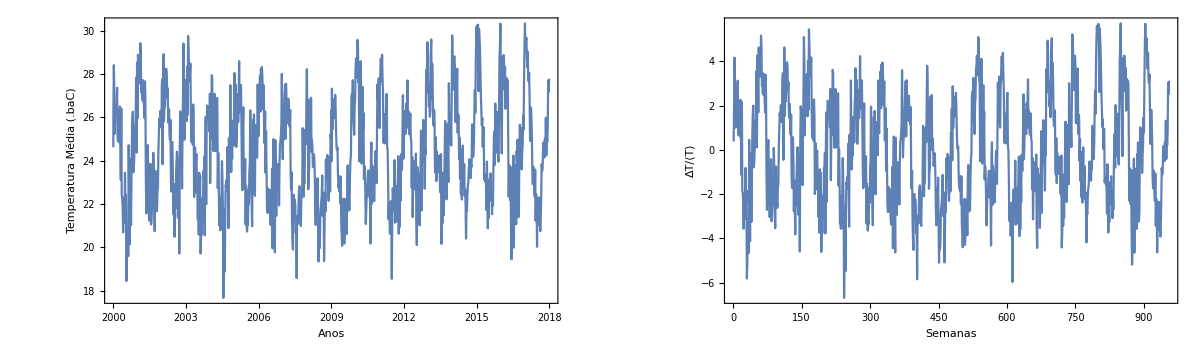

```mathematica
{DateListPlot[temp,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Temperatura Média (.baC)",None},{"Anos","Série Original"}},FrameTicks->{Automatic,{{"2000","2003","2006","2009","2012","2015","2018"},None}}],
ListLinePlot[tempDetrended,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"ΔT/⟨T⟩",None},{"Semanas","Série de Diferenças"}},Axes->False]
}//GraphicsRow
```

Após remover tendências lineares da série original, olhamos para o espectro da série de diferenças. É possível ver um pico altamente dominante. Usamos as funções definidas na seção anterior para identificar a frequência responsável por esse pico, fazer um ajuste não-linear de uma função do senoidal e remover tal função da série de diferenças.

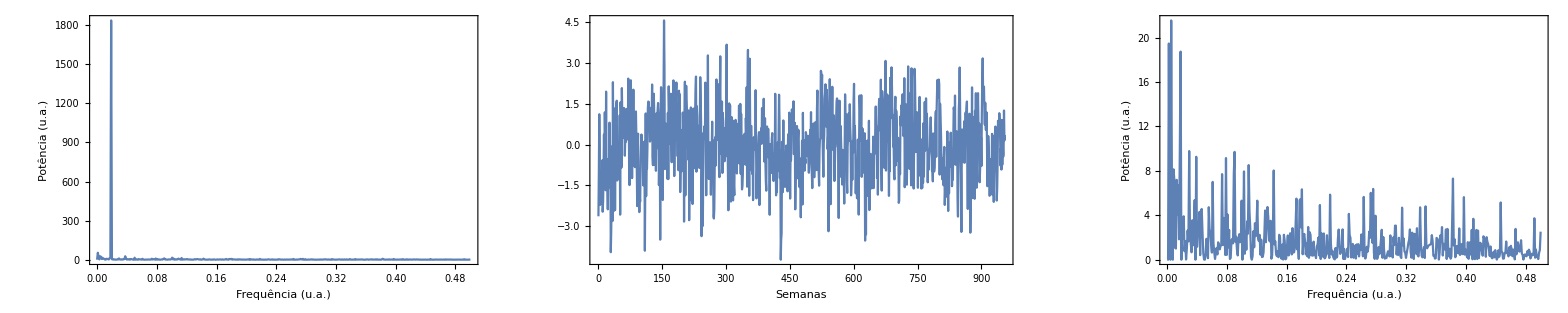

```mathematica
{tempSinusoidalComponents1,tempSC1}=removingSinusoidalComponents[tempDetrended,10,1,0];
{Periodogram[tempDetrended,PlotRange->All,ScalingFunctions->"Absolute",Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)",None},{"Frequência (u.a.)","Espectro - tempDetrended"}}],
ListLinePlot[tempSC1,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série sem componentes senoidais 1"}}],
Periodogram[tempSC1,PlotRange->All,ScalingFunctions->"Absolute",Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)",None},{"Frequência (u.a.)","Espectro - tempSC1"}}]}//GraphicsRow
```

Ainda é possível remover algumas outras frequências de menor potência, porém não é possível eliminar uma quantidade suficiente para que a série fique suficientemente estacionária. Isso é feito em dois passos, mostrados abaixo.

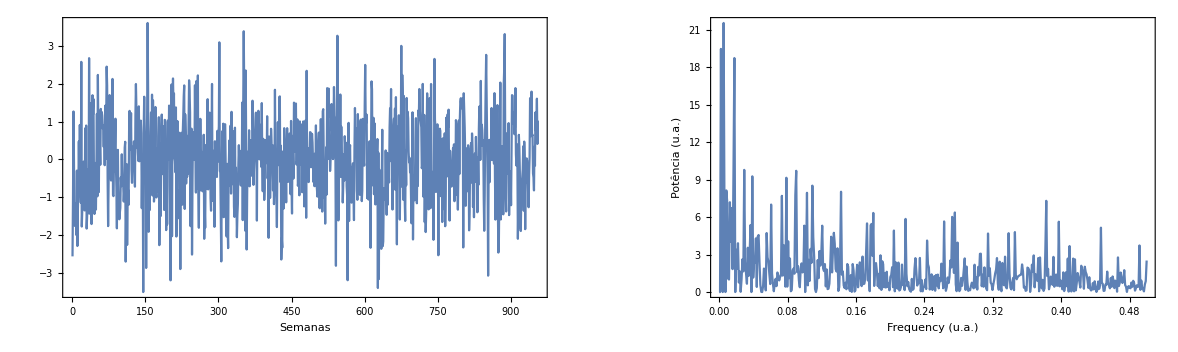

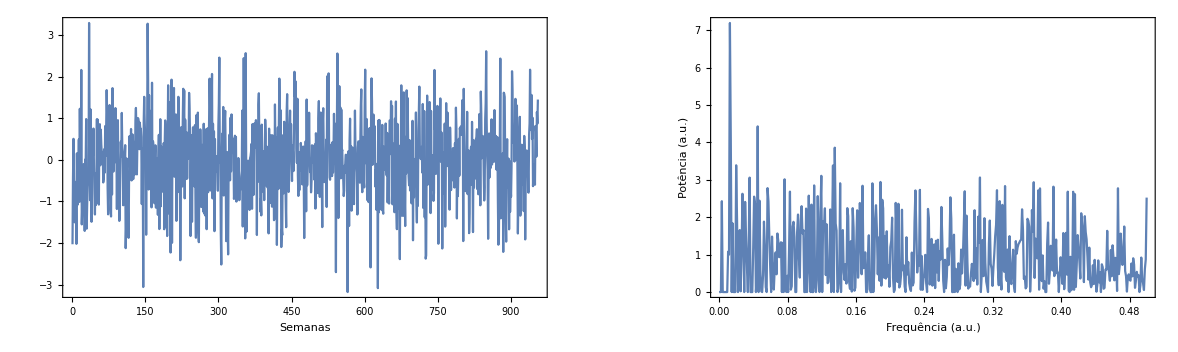

```mathematica
{tempSinusoidalComponents2,tempSC2}=removingSinusoidalComponents[tempSC1,5];
{tempSinusoidalComponents3,tempSC3}=removingSinusoidalComponents[tempSC2,3];
{ListLinePlot[tempSC2,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série sem componentes senoidais 2"}}],
Periodogram[tempSC1,PlotRange->All,ScalingFunctions->"Absolute",Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)",None},{"Frequency (u.a.)","Power Spectrum - tempSC2"}}]
}//GraphicsRow
{ListLinePlot[tempSC3,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série sem componentes senoidais 3"}}],
Periodogram[tempSC3,PlotRange->All,ScalingFunctions->"Absolute",Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (a.u.)",None},{"Frequência (a.u.)","Power Spectrum - tempSC3"}}]}//GraphicsRow
```

A natureza oscilatória das funções de correlação, correlação parcial e covariância abaixo indicam que ainda há na série final alguma contribuição senoidal importante que não pode ser removida. Isto mostra que a série não está exatamente no regime estacionário fraco, i.e. primeiros e segundos momentos estacionários. O fato de os segundos momentos ainda apresentarem um claro comportamento oscilatório é particularmente crucial para o mal funcionamento do modelo.

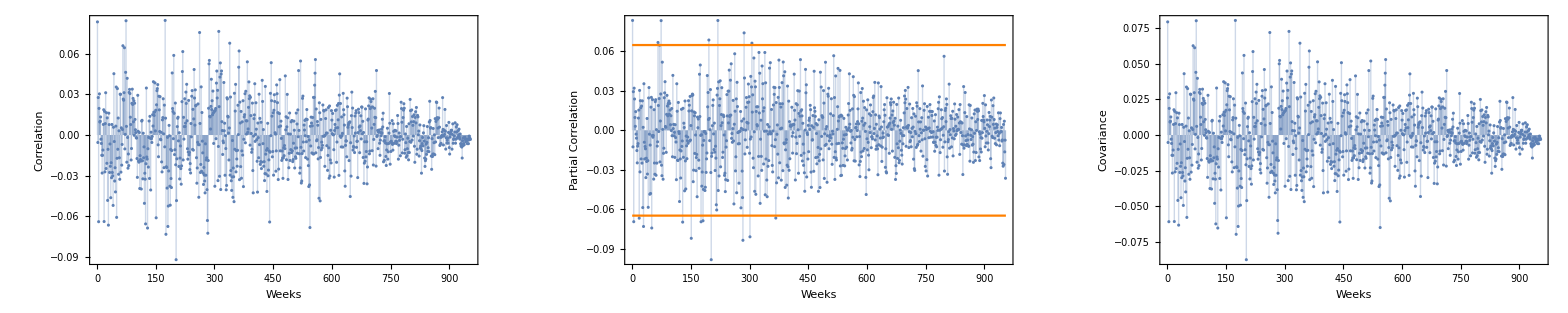

```mathematica
{ListPlot[CorrelationFunction[tempSC3,{1,Length@tempSC2-1}],Filling->Axis,PlotRange->{{0,Length@tempSC3-1},All},Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Correlation",None},{"Weeks","tempSC3"}}],
Show[{ListPlot[PartialCorrelationFunction[tempSC3,{1,Length@tempSC3-1}],Filling->Axis,PlotRange->{{0,Length@tempSC3-1},All},Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Partial Correlation",None},{"Weeks","tempSC3"}}],Plot[{y=2./√Length[tempSC3],y=-2./√Length[tempSC3]},{x,0,Length[tempSC2]},PlotStyle->Orange]}],
ListPlot[CovarianceFunction[tempSC3,{1,Length@tempSC2-1}],Filling->Axis,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Covariance",None},{"Weeks","tempSC3"}}]
}//GraphicsRow
```

Ainda assim, pode-se utilizar uma rede neural para tentar extrair alguma propriedade da série residual. Como na literatura de redes neurais ainda não há métodos determinísticos para optimização dos hiperparâmetros da rede, os parâmetros abaixo foram determinados através de tentativa e erro. Uma boa prática com relação ao número de inputs é observar quais correlações parciais são relevantes , o que aqui é definido como correlações parciais com valores acima de 2/(√Length[tempSC3]). Aqui, o número 29 é bom pois é grande o suficiente para representar um pouco mais de um semestre de correlações, porém não tão grande a ponto de pequenas correlações serem suavizadas por comportamentos de longo prazo. Outra boa prática é escolher o número de neurônios tal que input > neurons > output.

```mathematica
tempNeurons=5;
tempInputNumber=29;
tempOutputNumber=1;
{tempTrain,tempTest}=sampleSplit[tempSC3,tempInputNumber];
tempBatchSize=1;
tempNetModel=neuralNetwork[tempSC3,tempNeurons,tempInputNumber,tempOutputNumber,tempTrain,tempTest,tempBatchSize];
```

Abaixo uma propriedade crucial do treinamento: a evolução da função loss em função das rodadas de treinamento. Função Loss é a norma Euclidiana tanto para set de treinamento quanto para set de teste (validation).

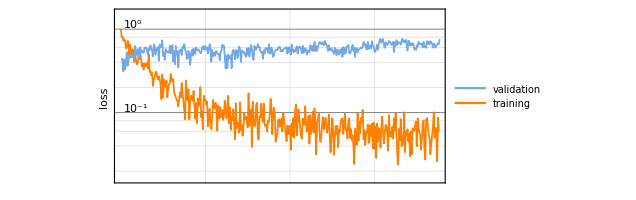

```mathematica
tempNetModel["LossEvolutionPlot"]
```

Pelo fato de a série não ser cíclica, i.e. tempSC3[[-1]] ≠ tempSC3[[1]], e pelo fato de na hora do treinamento estarmos dividindo a série tempSC3 em sequências de tempInputNumber valores de input levando a um valor de output, tempos que alguns valores finais da série não entram em qualquer um dos sets train ou test. Assim, usamos estes pontos numa vistos antes pela rede para analisarmos como a rede se comporta na previsão de pontos futuros. Abaixo são calculados tempFuturePoints pontos futuros, que são mostrados em um gráfico junto com a série tempSC3.

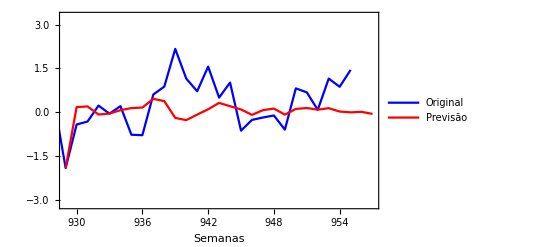

```mathematica
tempFuturePoints=tempInputNumber;
tempTrained = Flatten[NestList[Rest[Append[#,tempNetModel["TrainedNet"][#]]]&,tempTest[[-1,1]],tempFuturePoints][[-2]]];
tempPlot=Thread[{Range[Length@tempSC3-Mod[Length@tempSC3,tempInputNumber+1]-1,Length@tempSC3-Mod[Length@tempSC3,tempInputNumber+1]+Length@tempTrained-2],tempTrained}];
ListLinePlot[{tempSC3,tempPlot},Joined->True,PlotLegends->{"Original","Previsão"},PlotRange->{{tempPlot[[1,1]],tempPlot[[-1,1]]},All},PlotStyle->{Blue,Red},Axes->False,
Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série Residual"}}
]
```

Podemos ver que o modelo é instável, não capturando a magnitude das amplitudes da série tempSC3. Pouquíssimos pontos futuros têm uma predição confiável. Abaixo mostro em um outro exemplo que uma série no regime estacionário apresenta resultados mais consistentes.

### Carga de Energia - Submercado Sudeste / Centro-Oeste

Vamos usar uma série disponibilizada pelo Operador Nacional do Sistema Elétrico (ONS). A série representa a carga de energia média por semana operacional para o submercado Sudeste / Centro-Oeste. Por “carga de energia” entenda-se demanda média requerida de uma instalação ou conjunto de instalações durante um período de referência. Sua unidade é o MWmed.

```mathematica
(*SetDirectory[NotebookDirectory[]];
cargaEnergiaRaw=Import["Sudeste_Carga_de_Energia.csv"];
cargaEnergia = Reverse[Rest[cargaEnergiaRaw[[All,9]]]]*)
cargaEnergia={20000.7595238,19703.20654761,19998.82559523,20105.58154761,19674.00595238,20121.22797619,20135.97619047,20427.24023809,20651.89404761,20644.42142857,20906.59636904,20445.24940476,21111.66190476,20854.40642857,20505.88898809,20719.61653726,20886.7597619,21112.31607142,20998.87380952,21136.64345238,21515.28511904,22453.20059523,22030.7720238,22711.79380952,22075.29803571,19297.72303571,19791.16244069,22772.34208315,22396.5129174,22627.28696422,24119.02095183,23214.61428435,22310.38541739,23970.9701782,24343.61898779,25311.89601133,25996.67499992,25673.80690457,24421.43196371,25471.68595279,25344.38720221,25786.27196571,25919.74089216,24933.81904792,25361.8475599,25365.73916617,24763.25351145,23510.47619049,24754.11029822,25307.4815461,24907.96779752,24304.7159515,24456.00833239,23828.22875038,23985.77020074,24346.02693104,24311.64143034,24817.70105512,25173.53258087,25374.65464291,25308.68613097,24444.60017899,24905.46976186,25802.43880987,24830.50327368,25999.34374976,27160.2417858,27268.03750082,27138.14684427,26883.49583447,25511.19810006,26002.3761304,26853.94458329,27234.34660712,27626.58029767,26512.01624967,26198.61565399,23856.51982199,23289.23339208,25813.62535544,25807.56761814,26319.03529681,25698.47238163,27049.44797695,27808.08869163,27211.9300003,27976.44922596,26114.37315368,27206.63821648,26885.34791588,26026.56297592,26672.38626837,26313.6151964,25087.20007173,25725.84998836,26429.87129749,25086.26267937,25417.83124879,25929.02797651,25078.53077517,25578.82529768,26030.28422612,24969.76124961,25223.5166087,25042.22904883,25150.26589263,24891.98636806,25403.48636957,25571.57374981,25974.0100601,25509.28672626,25339.7949998,25636.83059533,25425.00851181,26168.85386802,25813.52738025,26940.93136936,26506.78517885,27160.15089282,25866.55750038,26723.10668689,26829.4856541,25677.55708012,27071.7242679,26760.91719254,27396.48017808,27536.52732017,27332.4706549,27849.29744165,24906.40488138,23710.37994014,25477.52892749,26856.12559616,26557.78511805,27432.31958298,28026.66190397,26638.75244012,27637.03190477,25503.20636954,27301.84904736,27891.78166769,27512.92178537,26842.87476203,27443.61351318,27047.5653589,27318.16559516,27587.01547643,26926.28077374,27067.14029795,26889.86648793,26541.39345139,26573.71148821,26650.60488036,25744.67315465,26424.22160645,26761.54785608,27119.70791999,26963.50040696,26767.89660735,26340.04749878,26294.64464324,26900.39529762,26733.67815432,27100.28422638,27914.17029715,27841.25357254,27390.42618999,28135.35422669,28862.3614881,29095.44913674,27473.62720278,27518.71744095,28354.02779945,28143.25392793,27982.58492411,28476.84243996,27573.6799394,28279.61119184,28264.27876146,28953.36107046,28277.02898888,27322.21779724,25698.99011932,26738.7677975,28439.89220298,28725.31500059,28128.45148609,27773.47523853,26067.44452232,28748.86089397,29793.40369059,29262.00303647,29403.59869118,30243.18351231,28729.84369003,28833.01422881,30408.95035723,30706.63452083,29255.99428587,28292.12839451,27270.19654985,28486.96619142,29193.76499862,27245.29625032,27382.02738096,27960.7585113,28237.69795291,27597.74125077,27561.41523721,27574.79821509,26992.89452287,27355.5757744,27347.88684483,27685.84827367,27931.18113064,28482.4269656,28585.26779712,29288.85293452,27766.26647023,28538.84730357,28365.0238869,27730.28750595,28718.1485238,29036.31643452,29418.45547101,29798.4388988,27464.78308928,28115.75996428,27823.81903571,29329.51755357,28965.38005952,28400.80321428,28636.21529761,28788.75092857,26578.86333333,27063.27005952,29169.79732142,30249.83755952,30882.21773809,29689.84771428,31056.04910119,29949.81783333,30851.3655238,28988.17969642,30812.54232142,30285.3072619,30890.73089285,30206.97315476,29562.40208333,29304.72291666,28058.48303571,29743.86779761,28141.20672619,28378.95053571,28070.42803571,28446.76773809,28758.41547619,28614.84934523,27848.2947619,28473.80071428,28453.67630952,28401.93613095,29137.86845238,28708.04176785,29210.46118452,28815.38279761,29656.05303571,30377.36505952,29319.02125,29285.39714285,27651.71,29770.02008333,29859.9338869,29006.07178571,29488.08069047,28853.65144642,29489.60440476,29131.86547619,29548.13928571,29450.72887681,28671.75488095,30256.9725,30910.60886904,30474.656875,30350.32488095,30975.25744047,28135.42607142,27148.58708333,30153.79839285,30252.00869047,30567.20458333,31135.90160714,31356.34589285,30825.115,29909.36154761,32098.44190476,32634.96535119,32900.16645833,32044.02547023,32979.43444642,32215.84515476,31178.66345238,31842.43523809,31844.88369047,28983.04357142,29989.47773809,30472.63970238,29961.20107142,29122.15928571,28458.1320238,29762.96892857,30034.38261904,29951.43160714,29620.6307738,29512.46857142,29840.39619047,30010.11041666,29268.7882738,30283.80238095,30388.61565476,30485.86204761,30988.4375,30614.80925,31013.63360714,32016.74095238,31740.6652738,31429.75489285,31818.42541666,32061.18263975,31623.00428571,32187.46839285,31441.69690476,30883.79755952,30810.79886904,31591.12047619,32464.37017857,32781.88119047,31713.04535714,28919.21720238,30027.96071428,31823.12440476,31971.03672619,30859.90936904,30315.53821428,28927.26683333,32339.75801785,32569.29089285,32131.06273809,33274.59732142,33037.03071428,31239.50839285,32191.53940476,32205.47773809,32233.40065476,32681.60785714,31289.81511904,31262.53375,30615.20505952,31025.40083333,30783.50041666,31503.2407738,30792.12773809,31794.5170238,31443.58023809,31285.89494047,31352.45428571,30640.32886904,30934.97404761,31639.98434523,31699.97422619,32154.84386904,32339.48136904,32997.3385119,32615.85767857,32188.82755952,32985.31619047,31922.74053571,31339.23291666,31741.52369047,31875.30040476,33397.9797619,32626.2250414,33620.67809523,32359.22017857,31709.37767857,30250.60034523,30458.77690476,30402.98660714,30871.8,28989.00547619,26603.14232142,25682.11630952,28309.09017857,31139.69928571,30203.11630952,30169.13684523,31569.4135119,31943.66625,31666.15214285,29924.17232142,33589.44422619,33029.33220238,31957.34392857,31290.02291666,31254.49029761,30455.81833333,30221.07071428,29053.41089285,29547.00583333,29435.31494047,30733.13392857,29755.41011904,30535.5775,29031.765,28756.74089285,28680.26267857,29534.71940476,29796.19482142,29566.91494047,29740.46065476,30087.38261904,30402.97422619,30696.54113095,30689.57761904,31493.2075,30487.17571428,31842.11208333,31311.94011904,32260.39583333,31751.65875,31782.51877857,32220.31595238,31099.65595238,32138.18012681,32424.91279761,32118.76482142,33309.79940476,33925.55154761,34997.80738095,34742.25190476,32860.64625,33180.42220238,31051.945,29669.29174367,32789.19810515,34508.58781057,34496.59566223,34231.86591086,35822.83763539,35927.0385119,33715.83738095,35999.2872619,33168.28059523,34843.01422619,35142.49744047,35320.44458333,33898.65107142,31933.93404761,32219.72232142,33510.18255952,34100.0435119,32842.47440476,31902.67714285,32323.46797619,32497.71398809,31260.22761904,31552.50291666,31711.19958333,32624.64166666,32208.07005952,32115.90791666,32687.30767857,32315.19428571,32556.40833333,32571.27744047,32590.58797619,32329.55791666,33653.35416666,34264.20011904,32508.33898809,34252.19303571,34538.24196428,34372.76017857,33621.15922619,31943.73982142,33640.8213561,33848.74285714,32518.2547619,33725.01571428,31999.5285119,34387.02761904,35492.5520238,35960.65619047,35617.90648809,34357.73053571,30786.89232142,32162.2845238,35190.33553571,35499.86619047,36435.17148809,37082.00940476,37498.34011904,37091.90161428,37272.9507738,35356.0220238,32635.18071428,35390.29380952,35048.36944866,36424.35699853,35000.14607142,35814.60345238,34477.50642857,34134.92654761,34019.87761904,34093.42880952,32906.08220238,33073.81190476,32773.9522619,32770.20172619,32410.33392857,32295.77113095,32566.51422619,32720.71678571,32775.55648809,33770.65910714,33399.1432738,33933.08892857,34529.44232142,35019.09035714,34437.45565476,34948.65892857,33952.65315476,34940.92267857,35133.93095238,35250.5297619,35299.6035119,35175.22922619,33743.72567028,34792.54005952,33094.30583333,35366.15321428,34302.08791666,35351.03172619,35507.16315476,35782.33285714,35986.83017857,36160.76875,32785.98559523,32570.21130952,34753.27446428,35926.8832738,36579.65517857,36066.35880952,38979.11589285,37489.85553571,35487.50994047,39233.84005952,38856.97773809,38336.97559523,37287.79875,37659.6525,36433.19232142,37254.0110119,37092.59208333,36001.97392857,33686.76854166,34515.80297619,34181.7135119,33405.7770238,34542.55773652,33943.91869066,33644.49571466,34498.15969009,33948.36111238,34123.10512576,33230.62428571,33257.77940476,34224.74,34641.89347823,34509.47757942,34727.90836233,34695.32330961,34422.93984838,34442.69067261,36402.11682142,37384.97261904,34696.72953571,36030.70168452,36397.11110714,35154.06048809,37082.36618892,37453.58524404,35143.83397619,33729.40200595,33781.18735266,35410.53972616,37354.1588869,38699.90879166,37628.80650595,35262.32119047,33984.33147619,37670.88000595,35380.15686309,36157.21656547,36501.87028571,36824.69440476,36491.26280357,40253.723625,39191.45417857,39305.92054761,39687.97711309,37080.85055952,36031.69597619,36510.58721428,36783.1120238,35315.55253571,34539.86519642,34735.46747023,34895.50036309,35311.71328571,34620.54791666,33643.14513052,34009.61618452,34642.05648214,35068.41466071,35143.75366071,34497.11054761,33294.74025595,34770.29799404,34533.38088095,34082.60558928,35608.30635714,35154.1402619,35265.40785714,35123.91510119,35517.17509523,35532.95209523,37037.15249404,36434.62645833,36586.4564609,34893.1957738,35989.67558333,37244.78740424,36378.47357142,35509.03358333,36824.01892857,37035.01875,36539.01079166,37970.7907738,37380.9982738,36122.21136904,33050.76148809,34725.28917261,39518.49151785,40004.35945238,39429.32548214,41276.20549404,42691.66942616,42476.40522023,39013.58194649,40570.55511738,37144.64811309,39426.0592131,41462.53524973,38309.74273809,39029.21613095,38770.67005952,36577.50189285,35482.77092857,33806.23902976,36188.68468452,34839.05475492,35680.60521368,34583.45723639,34337.44567948,34888.36278709,33420.11281048,33663.2824375,33977.80869047,33799.1653988,33763.00304761,33807.37542261,33414.59251785,34213.71848214,34239.46658333,34472.39548495,35137.35106778,34992.98330357,35266.67420238,36147.31657142,35789.28582738,36349.30652976,34987.90343452,38763.24217261,36982.07374042,35970.71961309,37590.62685119,36497.28316071,34228.50720238,36891.12183333,36321.20342857,36633.3412619,36243.07779166,33971.03323349,34907.69307142,39016.76850595,42603.02864285,42644.26441071,40352.74279761,39508.13106494,39290.81472624,37251.7434891,40638.60432011,39369.8382854,38599.30350595,38187.66911904,37153.06003571,36828.92550595,35916.14306595,36750.83586029,35785.45663095,33572.67144642,33573.0600238,33205.81014285,33231.2902619,34322.70086309,32257.86771965,33231.16367261,33232.63759523,31770.62798214,31955.95373809,31963.14806547,33292.82291666,32927.8543869,33121.76491071,33764.88036904,33849.90357738,34439.74407753,34266.0463988,34489.26770238,33163.32771428,35003.6100238,37624.22804761,36540.91971428,36235.35691666,36656.19445238,37645.20766925,35882.8958988,35516.23842857,37103.92740476,37066.129875,36118.89272023,36201.01349404,36502.93122023,38240.97705952,36019.00413095,34442.68216468,36265.28621284,38242.21717639,35315.05839384,37654.96776066,39941.29675164,37879.49124582,40016.13750369,39746.54203638,38510.26266601,39000.72143316,37926.00540911,38022.56668545,38792.27283975,39264.02741727,39515.41707264,38347.90520287,36596.1329918,33404.58032885,35286.78054761,34304.37018452,33230.0188988,34493.33985714,34313.22548214,32143.26667261,32751.93532738,32545.18498809,33171.69551785,33784.54874404,33010.5626488,33557.71907738,33535.14735774,34133.90023214,34592.39319047,33772.40655952,34818.15430952,33669.89548214,35663.99482142,35143.86019047,34275.18464285,33285.51841666,33929.38422023,38131.757956,36571.9917619,34301.52910119,35752.20181547,33262.82960714,33809.64958333,35654.72642857,35893.85264285,35900.0931369,35131.98815476,36453.26892857,38143.383625,40404.47385714,38472.59243089,38465.50527976,39579.36643452,39536.10522023,40799.10110714,42088.4325119,37953.97697619,40866.24026785,41063.18275595,37517.40092857,37505.20795833,37290.23679761,36867.14784523,35395.46297619,35290.328,33069.43648809,34546.31594047,34775.80164821,34701.31699404,33954.08085714,35100.47394642,33290.69108928,33486.33482142,33209.51320238,32500.01973809,32782.49173809,32652.4530119,33002.79763095,32893.4751369,33514.81649404,34039.51580952,33560.10090476,34071.49717261,33511.46267857,36037.86963511,36639.16445892,36252.25720833,35257.79898214,36982.24827976,37459.67450698,36726.10018452,35231.0382619,35733.66041071,35773.30320238,35785.73924404,36621.61079761,36536.85075595,37303.42033333,38392.05610327,35874.70301785,35315.06515476,37228.58968452,40034.82309523,41921.83280357,39052.16291666,38253.29732142,37777.30070238,39529.58460714,39243.86898809,40467.07914285,40773.49663095,40437.15958928,38604.61404166,38392.76434523};
```

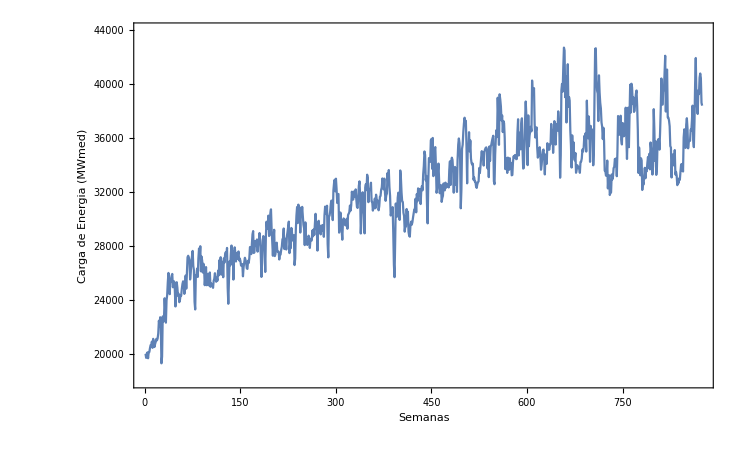

```mathematica
ListLinePlot[cargaEnergia,PlotRange->{All,{18000,44000}},Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Carga de Energia (MWmed)",None},{"Semanas","Submercado Sudeste / Centro-Oeste"}}]
```

De novo passamos pelo processo de tornar a série estacionária. Aqui já removo tendências lineares e senoidais de uma vez.

```mathematica
Clear[energiaLinearTrend,energiaS1,energiaSinusoidalComponents1,energiaS2,energiaSinusoidalComponents2,energiaS3];
```

```mathematica
{energiaLinearTrend,energiaS1}=detrending[differencing[cargaEnergia]];
{energiaSinusoidalComponents1,energiaS2}=removingSinusoidalComponents[energiaS1,0.003,1];
{energiaSinusoidalComponents2,energiaS3}=removingSinusoidalComponents[energiaS2,0.0025,1];
```

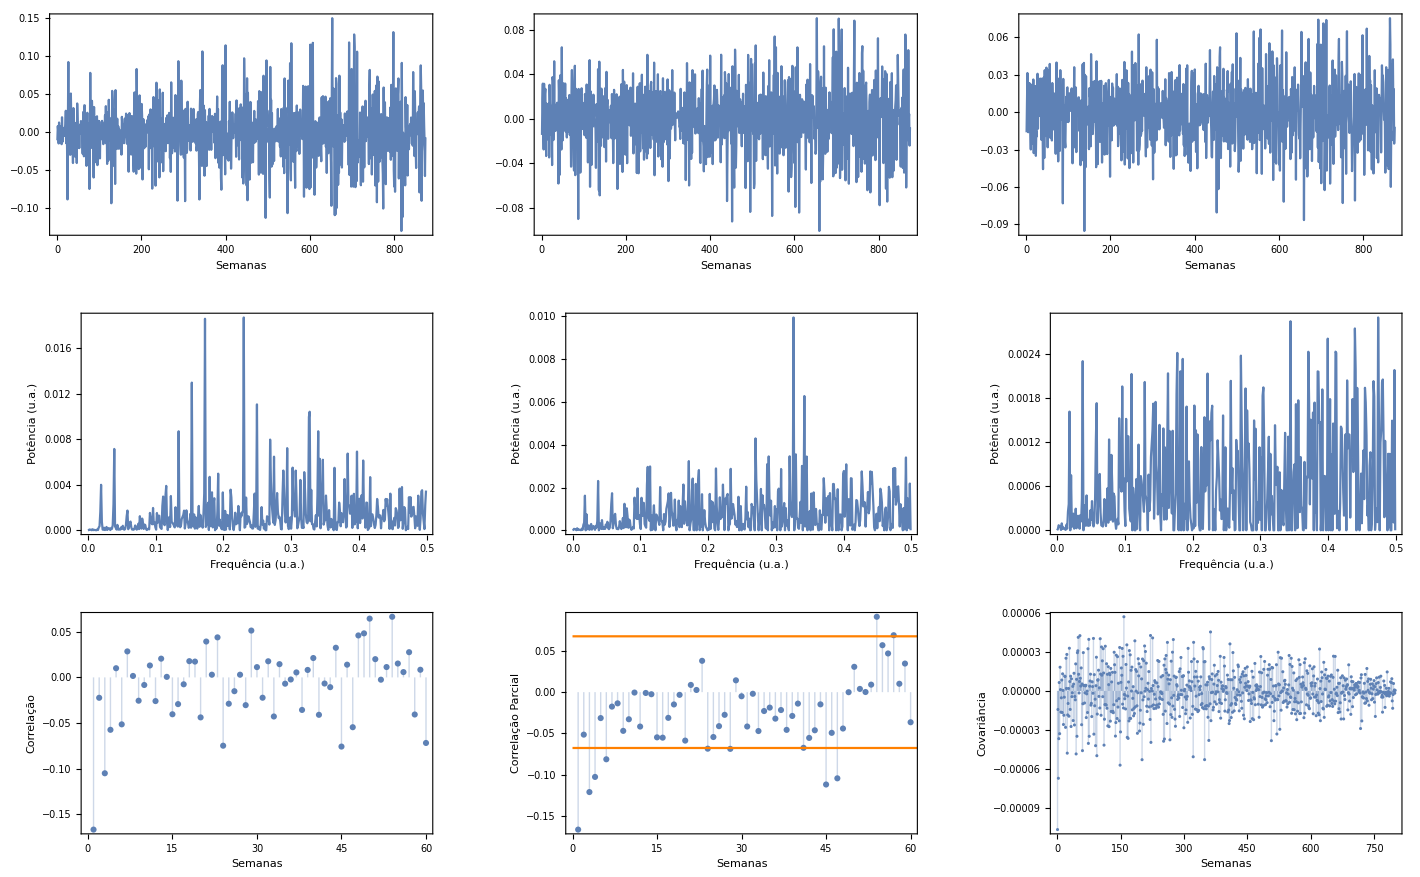

```mathematica
{{ListLinePlot[energiaS1,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série s_1 sem tendência linear"}}],ListLinePlot[energiaS2,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série s_2 sem primeiras componentes senoidais"}}],ListLinePlot[energiaS3,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série final s_3"}}]},
{ListLinePlot[periodogramFrequency[energiaS1,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_1"}}],
ListLinePlot[periodogramFrequency[energiaS2,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_2"}}],
ListLinePlot[periodogramFrequency[energiaS3,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_3"}}]},
{ListPlot[CorrelationFunction[energiaS3,{1,60}],Filling->Axis,Axes->False,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Correlação", None},{"Semanas","s_3"}}],
Show[{ListPlot[PartialCorrelationFunction[energiaS3,{1,60}],Filling->Axis,Axes->False,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Correlação Parcial", None},{"Semanas","s_3"}}],Plot[{y=2./√Length[energiaS3],y=-2./√Length[energiaS3]},{x,0,Length@energiaS3},PlotStyle->Orange]}],
ListPlot[CovarianceFunction[energiaS3,{1,800}],Axes->False,PlotRange->All,Filling->Axis,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Covariância", None},{"Semanas","s_3"}}]}}//GraphicsGrid
```

Aqui de novo cheguei a esses parâmetros através de tentativa e erro. Um passo futuro seria verificar exatamente o espaço de parâmetros através de análise do erro quadrático médio em função de cada parâmetro.

```mathematica
energiaNeurons=5;
energiaInputNumber=27;
energiaOutputNumber=1;
{energiaTrain,energiaTest}=sampleSplit[energiaS3,energiaInputNumber];
energiaBatchSize=1;
energiaNetModel=neuralNetwork[energiaS3,energiaNeurons,energiaInputNumber,energiaOutputNumber,energiaTrain,energiaTest,energiaBatchSize];
```

Aqui mostro gráfico da predição para tantos pontos futuros quanto inputs. Vemos que não há perda de amplitude. Ainda assim a previsão para Semanas → ∞ não é confiável pois, para pontos muito distantes, rede perde capacidade de predizer ruídos e a característica oscilatória da predição se torna muito dominante, escondendo outros features.

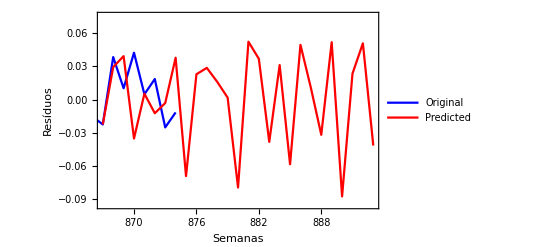

```mathematica
energiaFuturePoints=energiaInputNumber;
energiaTrained = Flatten[NestList[Rest[Append[#,energiaNetModel["TrainedNet"][#]]]&,energiaTest[[-1,1]],energiaFuturePoints][[-2]]];
energiaPlot=Thread[{Range[Length@energiaS3-Mod[Length@energiaS3,energiaInputNumber+1]-1,Length@energiaS3-Mod[Length@energiaS3,energiaInputNumber+1]+Length@energiaTrained-2],energiaTrained}];
ListLinePlot[{energiaS3,energiaPlot},Joined->True,PlotLegends->{"Original","Predicted"},PlotRange->{{energiaPlot[[1,1]],energiaPlot[[-1,1]]},All},PlotStyle->{Blue,Red},Axes->False,
Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Resíduos",None},{"Semanas","Série Residual"}}
]
```

Podemos somar à predição acima todas as componentes extraídas da série de diferenças s_1 . Basta pegarmos os modelos lineares e senoidais ajustados anteriormente e calcularmos suas contribuições para cada instante de tempo. Assm, gráfico abaixo mostra o comportamento da previsão das diferenças semanais de carga de energia.

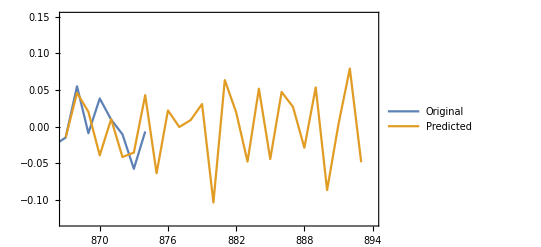

```mathematica
energiaTrend=Table[energiaLinearTrend[i],{i,energiaPlot[[1,1]],energiaPlot[[-1,1]]}] ;
energiaCS1=Table[Sum[energiaSinusoidalComponents1[[k]][i],{k,1,Length@energiaSinusoidalComponents1}],{i,energiaPlot[[1,1]],energiaPlot[[-1,1]]}];
energiaCS2=Table[Sum[energiaSinusoidalComponents2[[k]][i],{k,1,Length@energiaSinusoidalComponents2}],{i,energiaPlot[[1,1]],energiaPlot[[-1,1]]}];
energiaFinalPrediction=Thread[{energiaPlot[[All,1]],energiaPlot[[All,2]]+energiaTrend+energiaCS1+energiaCS2}];
ListLinePlot[{energiaS1,energiaFinalPrediction},PlotRange->{{energiaFinalPrediction[[1,1]],energiaFinalPrediction[[1,1]]+energiaFuturePoints},All},PlotLegends->{"Original","Predicted"},Frame->True,FrameStyle->Directive[18,Thick]]
```

Modelo se comporta significativamente bem para uma quantidade razoável de pontos futuros, o que é o objetivo final. Ainda falta fazer uma análise mais profunda de erros médios.

### Preço de Liquidação de Diferenças (PLD) - Submercado Sudeste / Centro-Oeste

Também oriunda do ONS, podemos analisar a série temporal para o Preço de Liquidações de Diferenças (PLD), i.e. o valor de mercado para comercialização de energia no mercado livre. Apesar de depender de outras séries temporais fortemente regulares (vazão de hidroelétricas da região, carga de energia semanal, etc...), esta série é interessante pois possui uma alta presença de irregularidades, e.g. mudanças legislativas, decisões executivas, teto e piso anuais, etc. Série obtida entre 06/07/2001 e 08/06/2018.

```mathematica
(*SetDirectory[NotebookDirectory[]];
precosRaw = Import["precos.csv"];
precos=Drop[Drop[precosRaw[[All,8]],188],-2]*)
precos={18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,18.33,19.74,25.03,33.31,47.99,42.25,49.38,45.01,28.09,18.33,31.39,29.72,24.37,26.15,32.72,35.26,34.13,28.46,27.13,37.36,32.94,47.1,38.93,31.76,27.42,23.09,35.56,39.44,41.24,47.98,47.48,31,32.06,35.5,31.8,18.33,18.33,18.33,18.33,16.92,16.92,16.92,38.35,66.75,57.13,82.97,33.04,36.78,37.85,16.92,16.92,34.37,22.46,20.78,17.06,16.92,35.76,48.9,55.75,55.29,59.6,61.31,64.5,73.91,71.6,90.66,86.34,85.07,90.49,103.63,98.44,96.45,94.53,125.24,123.42,115.5,123.32,127.89,105.57,112.73,81.51,80.71,69.65,94.81,68.65,79.27,85.75,79.07,69.47,50.36,35.89,34.04,23.55,17.59,17.59,17.59,17.59,17.59,17.59,17.59,17.59,17.59,17.59,17.59,17.59,62.58,53.76,55.25,54.7,35.79,43.12,48.63,118.08,101.85,114.6,74.73,81.49,138.89,141.55,130.1,116.3,57.95,28.31,27.21,33.88,56.58,128.1,130.81,147.26,186.16,165.13,172.08,205.54,209.7,237.66,223.89,181.3,150.54,169.19,189.25,212.2,200.48,199.76,247.01,472.21,569.59,569.59,550.28,253.32,122.33,155.84,207.36,137.23,129.66,173.39,63.99,82.27,115.62,68.18,15.47,39.19,28.48,15.47,33.45,49.34,76.12,76.03,69.88,76.72,88.11,91.32,102.53,110.12,145.35,138.25,117.49,77.05,69.38,93.25,105.62,118.04,120.97,100.23,97.53,74.28,93.2,98.71,103.73,115.28,109.17,91.04,95.35,103.42,113.15,91.34,74.1,28.13,62.27,137.52,108.4,65.15,61.44,43.08,16.31,59.91,80.7,106.95,94.06,105.13,16.31,49.12,37.93,45.12,45.76,36.21,36.1,36.99,37.59,34.97,40.8,42.68,51.6,38.84,31.28,20.73,21.45,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,16.31,12.8,12.8,12.8,12.8,12.8,12.8,12.8,12.8,23.28,12.8,12.8,35.05,37.15,12.8,12.8,23.26,22.09,22.35,22.87,32.43,34.49,56.07,59.9,59.49,65.43,99.67,102.29,95,78.15,71.36,104.64,124.16,114.95,122.27,104.53,124.43,115.68,130.72,167.47,135.97,112.7,140.34,140.62,147.15,117.68,125.45,98.34,77.56,84.74,72,61.98,52.44,67.24,12.08,14.97,21.29,12.08,36.79,52.67,60.88,77.47,12.08,18.77,12.08,12.08,12.08,12.08,12.08,12.08,15.31,13.54,15.11,16.9,29.96,32.73,34.63,29.23,29.7,27.48,22.96,20.79,18.8,22.98,15.68,17.34,23.41,15.9,16.73,20.25,22.83,23.61,41.99,42.75,37.48,22.95,37.73,42.94,39.01,43.94,61.97,49.68,34.08,44.38,39.71,45.31,28.57,12.2,12.2,12.2,35.45,53.86,62.2,65.99,94.84,133.72,139.53,130.51,185.44,186.15,196.83,189.19,188.82,179.28,168.5,188.99,176.42,146.19,146.14,101.16,74.33,54.83,94.11,106.01,103.37,87.12,105.35,115.67,128.01,137.01,173.5,180.47,188.6,185.8,173.98,240.08,319.75,284.61,360.38,427.54,449.61,314.35,307.41,198.54,264.94,179.69,341.57,338.63,554.82,336.55,478.43,298.14,171.72,153.88,209.35,306.3,368.69,337.57,336.68,316.99,298.76,186.05,147.86,126.38,275.05,339.57,354.26,348.98,353.44,320.57,179.63,188.14,162.16,94.3,102.84,120.51,125.7,151.57,164.62,143.77,169.16,153.23,255.16,264.93,271.58,250.1,260.29,227.93,237.72,242.2,305.29,308.11,316.09,329.82,353.79,302.28,270.33,303.81,293.94,249.92,280.22,384.02,409.38,480.64,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,822.83,777.23,822.83,822.83,806.9,551.09,237.76,335.59,314.63,314.63,535.31,613.57,686.2,576.78,797.56,643.96,688.35,684.99,717.91,688.25,757.1,735.21,650.71,680.48,790.39,822.83,822.83,822.83,822.83,822.83,822.83,547.99,673.67,644.18,658.73,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,388.48,364.49,369.33,375.73,352.18,357.6,368.82,309.5,222.38,98.33,112.52,115.36,127.05,133.16,136.11,267.9,240.36,193.63,218.15,198.83,205.88,197.57,194.1,204.74,219.09,195.18,179.31,174.05,141.86,123.83,101.63,132.45,48.15,42.5,32.46,30.25,30.25,30.25,30.25,30.25,30.25,30.25,47.76,30.25,30.25,40.26,41.71,46.5,50.42,49.38,84.7,77.73,70.19,70.62,56.79,55.57,53.75,54.1,70.35,79.62,83.87,77.64,74.45,114.5,114.78,112.47,90.36,126.11,129.51,133.94,136.9,139.47,148.67,207.74,210.48,189.23,160.74,229.16,174.71,180.54,167.7,150.08,140.71,100.4,119.78,141.27,113.03,138.99,98.62,126.7,127.5,99.46,110.5,118.69,129.74,183,182.02,233.55,215.21,230.14,415.78,349.73,344,326.72,437.61,445.46,458.7,463.56,33.68,33.68,33.68,83.87,89.66,231.5,249.75,261.75,264.53,506.77,533.82,508.64,493.79,442.35,488.05,533.82,533.82,533.82,533.82,533.82,533.82,533.82,533.82,464.57,476.7,443.38,206.09,218.1,212.08,271.76,245.49,193.6,173.51,158.66,184.6,166.66,172.33,167.11,205.39,196.86,219.06,230.72,215.34,223.03,40.16,79.96,118.17,131.04,209.5,293.92,313.62,327.41};
```

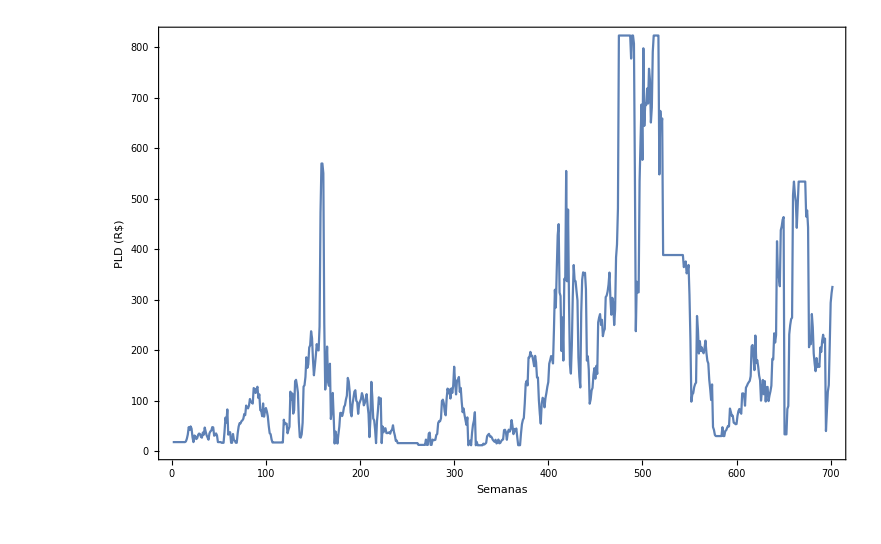

```mathematica
ListLinePlot[precos,PlotRange->{All,All},Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"PLD (R$)",None},{"Semanas","Submercado Sudeste / Centro-Oeste"}}]
```

Podemos fazer as mesmas exclusões de tendências lineares e senoidais, porém não é possível levar em conta as irregularidades de uma forma que não seja ad-hoc. Isto não foi feito aqui pois necessitaria de um histórico completo das mudanças legislativas ocorridas no período.

```mathematica
{precosLinearTrend,precosS1}=detrending[differencing[precos]];
{precosSinusoidalComponents1,precosS2}=removingSinusoidalComponents[precosS1,0.3,1];
{precosSinusoidalComponents2,precosS3}=removingSinusoidalComponents[precosS2,0.18,1];
```

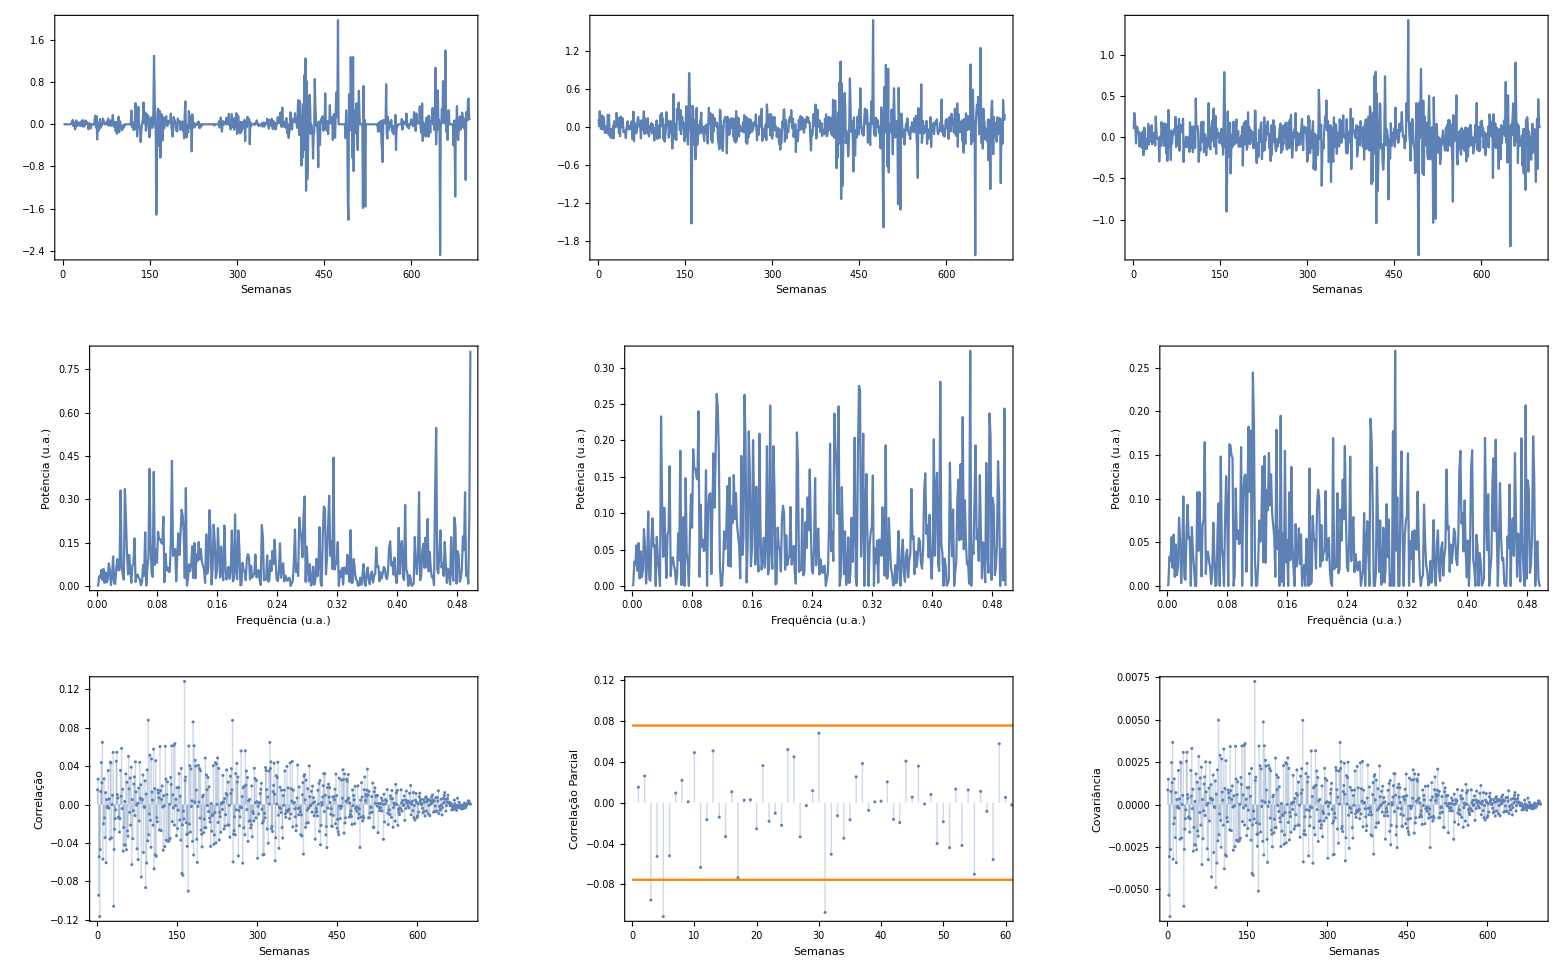

```mathematica
{{ListLinePlot[precosS1,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série s_1 sem tendência linear"}}],ListLinePlot[precosS2,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série s_2 sem primeiras componentes senoidais"}}],ListLinePlot[precosS3,PlotRange->All,Axes->False,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{None,None},{"Semanas","Série final s_3"}}]},
{ListLinePlot[periodogramFrequency[precosS1,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_1"}}],
ListLinePlot[periodogramFrequency[precosS2,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_2"}}],
ListLinePlot[periodogramFrequency[precosS3,1],PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Potência (u.a.)", None},{"Frequência (u.a.)","Espectro - s_3"}}]},
{ListPlot[CorrelationFunction[precosS3,{1,Length@precosS3-1}],Filling->Axis,Axes->False,PlotRange->All,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Correlação", None},{"Semanas","s_3"}}],
Show[{ListPlot[PartialCorrelationFunction[precosS3,{1,Length@precosS3-1}],Filling->Axis,Axes->False,PlotRange->{{0,60},All},Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Correlação Parcial", None},{"Semanas","s_3"}}],Plot[{y=2./√Length[precosS3],y=-2./√Length[precosS3]},{x,0,Length@precosS3},PlotStyle->Orange]}],
ListPlot[CovarianceFunction[precosS3,{1,Length@precosS3-1}],Axes->False,PlotRange->All,Filling->Axis,Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Covariância", None},{"Semanas","s_3"}}]}}//GraphicsGrid
```

Treinamento da série residual s_3

```mathematica
precosNeurons=5;
precosInputNumber=31;
precosOutputNumber=1;
{precosTrain,precosTest}=sampleSplit[precosS3,precosInputNumber];
precosBatchSize=1;
precosNetModel=neuralNetwork[precosS3,precosNeurons,precosInputNumber,precosOutputNumber,precosTrain,precosTest,precosBatchSize];
```

Como no caso de Temperaturas Médias, previsão obtida pela rede neural é altamente não confiável. Aqui, além de a série não estar exatamente em estado estacionário fraco ( covariâncias ∼10^-3), as irreegularidades previnem qualquer tentativa de predição dos resíduos não-lineares de forma estatisticamente confiável.

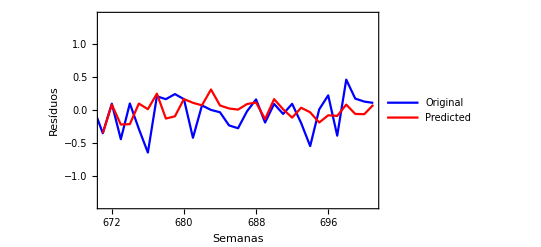

```mathematica
precosFuturePoints=precosInputNumber;
precosTrained = Flatten[NestList[Rest[Append[#,precosNetModel["TrainedNet"][#]]]&,precosTest[[-1,1]],precosFuturePoints][[-2]]];
precosPlot=Thread[{Range[Length@precosS3-Mod[Length@precosS3,precosInputNumber+1]-1,Length@precosS3-Mod[Length@precosS3,precosInputNumber+1]+Length@precosTrained-2],precosTrained}];
ListLinePlot[{precosS3,precosPlot},Joined->True,PlotLegends->{"Original","Predicted"},PlotRange->{{precosPlot[[1,1]],precosPlot[[-1,1]]},All},PlotStyle->{Blue,Red},Axes->False,
Frame->True,FrameStyle->Directive[18,Thick],FrameLabel->{{"Resíduos",None},{"Semanas","Série Residual"}}
]
```